```mathematica
b={0.5,0.6,0.7,0.8}
```

{0.5,0.6,0.7,0.8}

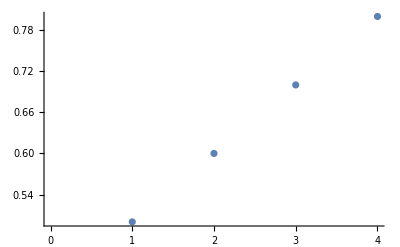

```mathematica
ListPlot[b]
```

```mathematica
b1={{0.,0.5},{1,0.6},{2,0.7},{3,0.8}}
```

{{0.,0.5},{1,0.6},{2,0.7},{3,0.8}}

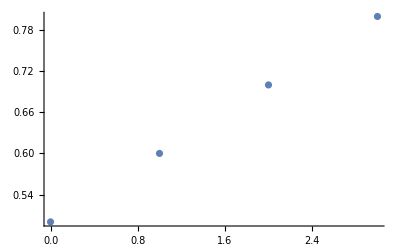

```mathematica
ListPlot[b1]
```

```mathematica
x={"Prob1","Prob2","Prob3"}
```

{Prob1,Prob2,Prob3}

```mathematica
numX={0.1,0.2,0.3}
```

{0.1,0.2,0.3}

```mathematica
numY={2,3,4}
```

{2,3,4}

```mathematica
numZ={5,6,7}
```

{5,6,7}

```mathematica
ex={0,0,0}
```

{0,0,0}

```mathematica
ey={2,3,4}
```

{2,3,4}

```mathematica
ez={6,7,8}
```

{6,7,8}

```mathematica
Tab1=Table[{x[[i]],numX[[i]],numY[[i]],numZ[[i]],ex[[i]],ey[[i]],ez[[i]],ScientificForm[Abs[numX[[i]]-ex[[i]]]],ScientificForm[Abs[numY[[i]]-ey[[i]]]],ScientificForm[Abs[numZ[[i]]-ez[[i]]]]},{i,1,3}]
```

{{Prob1,0.1,2,5,0,2,6,1.×10^-1,0,1},{Prob2,0.2,3,6,0,3,7,2.×10^-1,0,1},{Prob3,0.3,4,7,0,4,8,3.×10^-1,0,1}}

```mathematica
Tab2=Prepend[Tab1,{"Problems","X","Y","Z","ex","ey","ez","ErrorX","ErrorY","ErrorZ"}]
```

{{Problems,X,Y,Z,ex,ey,ez,ErrorX,ErrorY,ErrorZ},{Prob1,0.1,2,5,0,2,6,1.×10^-1,0,1},{Prob2,0.2,3,6,0,3,7,2.×10^-1,0,1},{Prob3,0.3,4,7,0,4,8,3.×10^-1,0,1}}

```mathematica
Tab3=Grid[Tab2,Spacings->{1,1},Frame->All]
```

Problems | X | Y | Z | ex | ey | ez | ErrorX | ErrorY | ErrorZ
Prob1 | 0.1 | 2 | 5 | 0 | 2 | 6 | 1.×10^-1 | 0 | 1
Prob2 | 0.2 | 3 | 6 | 0 | 3 | 7 | 2.×10^-1 | 0 | 1
Prob3 | 0.3 | 4 | 7 | 0 | 4 | 8 | 3.×10^-1 | 0 | 1

```mathematica
Clear[x,y,X,Y]
```

```mathematica
"NEWTON RAPHSON";
```

```mathematica
f[x_]=2x^3-x-11
```

-11-x+2 x^3

```mathematica
x[0]=1; h=0.1
```

1

```mathematica
v=Do[Print[x[n]=x[n-1]-f[x[n-1]] h/f'[x[n-1]] h//N],{n,1,5}]
```

1.5

1.615

1.68651

1.73463

1.76829

```mathematica
"Euler Method";
```

```mathematica
f[x_,y_]=x^2-2 x+1   ;y[0]=1; h=0.1
```

0.1

```mathematica
Do[Print[y[n]=N[y[n-1]+h f[x[n-1],y[n-1]]]],{n,1,5}]
```

1.

1.025

1.06282

1.10995

1.16392

```mathematica
f[x_,y_]=1 -y  ;y[0]=0; h=0.1
```

0.1

```mathematica
Do[Print[y[n]=N[y[n-1]+h f[x[n-1],y[n-1]]]],{n,1,5}]
```

0.1

0.19

0.271

0.3439

0.40951